```mathematica
f[x_]:=Sqrt[x^2+9]-3
g[x_]:=x^2/(Sqrt[x^2+9]+3)
X=8^(-Range[10])
```

{1/8,1/64,1/512,1/4096,1/32768,1/262144,1/2097152,1/16777216,1/134217728,1/1073741824}

```mathematica
TableForm[Transpose[{N[X], N[f[X]], N[g[X]]}]]
```

0.125 | 0.00260304 | 0.00260304
0.015625 | 0.0000406898 | 0.0000406898
0.00195313 | 6.35783×10^-7 | 6.35783×10^-7
0.000244141 | 9.93411×10^-9 | 9.93411×10^-9
0.0000305176 | 1.5522×10^-10 | 1.5522×10^-10
3.8147×10^-6 | 2.42517×10^-12 | 2.42532×10^-12
4.76837×10^-7 | 3.77476×10^-14 | 3.78956×10^-14
5.96046×10^-8 | 4.44089×10^-16 | 5.92119×10^-16
7.45058×10^-9 | 0. | 9.25186×10^-18
9.31323×10^-10 | 0. | 1.4456×10^-19

```mathematica
F={2.603054046631`200*^-3,4.076957702637`200*^-5,7.152557373047`200*^-7,0.000000000000`200*^0,0.000000000000`200*^0,0.000000000000`200*^0,0.000000000000`200*^0,0.000000000000`200*^0,0.000000000000`200*^0,0.000000000000`200*^0}
G={2.603037282825`200*^-03,4.068982525496`200*^-05,6.357827828651`200*^-07,9.934107758625`200*^-09,1.552204337285`200*^-10,2.425319277008`200*^-12,3.789561370325`200*^-14,5.921189641133`200*^-16,9.251858814270`200*^-18,1.445602939730`200*^-19}
```

{0.002603054046631,0.00004076957702637,7.152557373047×10^-7,0.,0.,0.,0.,0.,0.,0.}

{0.002603037282825,0.00004068982525496,6.357827828651×10^-7,9.934107758625×10^-9,1.552204337285×10^-10,2.425319277008×10^-12,3.789561370325×10^-14,5.921189641133×10^-16,9.25185881427×10^-18,1.44560293973×10^-19}

{-6.4081110593441328310341863495590044419837727963747117106284940401421397133142783665490395473348628313350049978477473983548549955006174292752083002096873300019000423273086958062199121759744802718×10^-6,-0.0019599198834930751140155247958968897809512075352952002674762820349353721083873326586899641667348342198541035471054284143634342299255395858887586988838056840199557750286458596959796378794266567999829,-0.1250001192092965797151524174679626638780831250021935394827876982005649931599779321077734330222064428484612436373301733552075055189257010469235724509620507178064215332481233184487028231818288415720328,1.,1.,1.,1.,1.,1.,1.}

{3.19832007144713541795072300515555174008565997721423813136899264049163811758114103100615086830747551634285785345853729861788689926095910016647134818030514922344744283768627558019771811261916555×10^-8,7.29425508458895316233375550530582058593385442432679681944498899673972363630086611740318350703275611827884456645397182357900561235200948586989776938236019917420343258244559985243931058856089876×10^-8,4.30478814377422654399157187966653210977236783568076490238579073422994789854926595674148402571829615202782025727844825955682969995429815040117724242993294699293642686356074172372931975835653567×10^-8,-3.14580495516962085085529138286170997786632912108556666095182528081478859331734345926683007100287679509690414172414776901972173251805975402745333371671369688422621988543177549640119483402876307×10^-8,-2.98281343369914140727131227856063974826777879262675322908697763686209762959855638464232083237482462047036448382749927450510611787900674145701850174163623173563071919497270279494209178995780358×10^-8,-2.98027457939948291699396272189080280557777066578595216232693711895972674140922739969181489012338761349615223388536933795979001777590446861077535687817229515538347049302179468192876599703720947×10^-8,-2.98023478900509452082934422918014594721824988736224909384688498267060900086458451999051303508044552283184583362579664676211156830042437713033319352608564071819903986742603947718370198656241139×10^-8,-2.98023733387367019676833235943095218402619556498745814750350413308816351906899471662150114279693988035144593099334928500992411057303803625677729489638622282374263251637270408879190473933207236×10^-8,-2.98023394645949791391249999976223086397722792199954389154387765138917692274978767966444661476949206966173887100938554080247853354131536000888545873296820777720218007847716104233992577398028087×10^-8,-2.9802555635859209836216833333332752842278590111951652741039204633430074505858268168614276440670551338847254888915789491251883842232772643316857583462968411977175027128063077832654022038062923×10^-8}

{-6.4081110593441328310341863495590044419837727963747117106284940401421397133142783665490395473348628313350049978477473983548549955006174292752083002096873300019000423273086958062199121759744802718×10^-6,-0.0019599198834930751140155247958968897809512075352952002674762820349353721083873326586899641667348342198541035471054284143634342299255395858887586988838056840199557750286458596959796378794266567999829,-0.1250001192092965797151524174679626638780831250021935394827876982005649931599779321077734330222064428484612436373301733552075055189257010469235724509620507178064215332481233184487028231818288415720328,None,None,None,None,None,None,None}

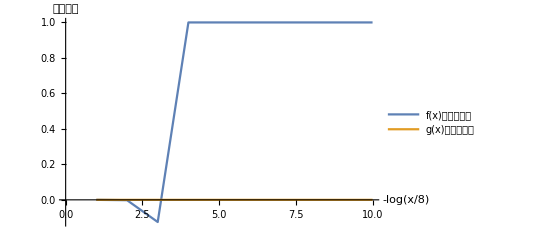

```mathematica
RelativeErrorF=(g[X]-F)/g[X]
RelativeErrorG = (g[X]-G)/g[X]
Catenate[{RelativeErrorF[[1;;3]],Table[None,7]}]
ListLinePlot[{RelativeErrorF,RelativeErrorG},PlotLegends->{"f(x)的相对误差","g(x)的相对误差"},AxesLabel->{-Log[x/8],"相对误差"}]
```

```mathematica
GivenData={4040.045551380452`50,-2759471.276702747`50,-31.64291531266504`50,2755462.874010974`50,0.0000557052996742893`50}
```

{4040.045551380452,-2.759471276702747×10^6,-31.64291531266504,2.755462874010974×10^6,0.0000557052996742893}

```mathematica
Total[GivenData]
NSum[GivenData[[i]],{i,5,1,-1},WorkingPrecision->100,PrecisionGoal->30]
```

8.66342893×10^-11

Part::pkspec1: 表达式 i 不能作为部分指定使用.

8.663428930000000000000000000000000000000000000007924171376797969861429731903798940057978262578165085×10^-11

```mathematica
Result = {1.025188136830`13*^-10,-1.564330887049`13*^-10,0.000000000000`13*^0}
```

{1.02518813683×10^-10,-1.564330887049×10^-10,0.}

```mathematica
(Total[GivenData]-Result)/Total[GivenData]
```

{-0.183351471009,2.805671749245,1.}

```mathematica
GivenData[[1]]+GivenData[[2]]
```

-2.755431231151366548×10^6

```mathematica
AccountingForm[-2.7554312311513665479999999999999999999999999999999999999999999999`49.99872832831561*^6]
```

(2755431.2311513665480000000000000000000000000000000)

```mathematica
-2755431.231151366`50+GivenData[[3]]
```

-2.75546287406667866504×10^6

```mathematica
AccountingForm[-2.7554628740666786650399999999999999999999999999999999999999999999`50.*^6]
```

(2755462.8740666786650400000000000000000000000000000)

```mathematica
-2755462.874066678`50+GivenData[[4]]
```

-0.000055704

```mathematica
AccountingForm[-0.0000557039999999999999999999999999999999999999999999999999`39.00466182260592]
```

(0.0000557040000000000000000000000000000000000)

```mathematica
-0.000055704`50 + GivenData[[5]]
```

1.2996742893×10^-9

```mathematica
AccountingForm[1.2996742893`45.066913083390716*^-9]
```

0.00000000129967428930000000000000000000000000000000000